```mathematica
Clear["Global`*"]
```

```mathematica
b = {b1,b2};
u = {u1,u2};
λ = {λ1,λ2};
A = DiagonalMatrix[λ]
```

{{λ1,0},{0,λ2}}

```mathematica
Solve[μ - Transpose[u].Inverse[-A - μ].b==0,μ]
```

{{μ→(-b1 u1+b2 u1+b1 u2-b2 u2-λ1 λ2-√(-4 (λ1+λ2) (b2 u2 λ1+b1 u1 λ2)+(b1 u1-b2 u1-b1 u2+b2 u2+λ1 λ2)^2))/(2 (λ1+λ2))},{μ→(-b1 u1+b2 u1+b1 u2-b2 u2-λ1 λ2+√(-4 (λ1+λ2) (b2 u2 λ1+b1 u1 λ2)+(b1 u1-b2 u1-b1 u2+b2 u2+λ1 λ2)^2))/(2 (λ1+λ2))}}

```mathematica
r = {λ1-> 1,λ2->5,b1-> 1,b2-> 1/100,u1->Sqrt[1-u2^2]};
```

```mathematica
a= 1/(2 (λ1+λ2))(b1 u1-b2 u1-b1 u2+b2 u2+λ1 λ2-√(-4 (λ1+λ2) (b2 u2 λ1+b1 u1 λ2)+(-b1 u1+b2 u1+b1 u2-b2 u2-λ1 λ2)^2))/.r
c = Transpose[u].b/.r
```

1/12 (5-(99 u2)/100+(99 √(1-u2^2))/100-√((-5+(99 u2)/100-(99 √(1-u2^2))/100)^2-24 (u2/100+5 √(1-u2^2))))

u2/100+√(1-u2^2)

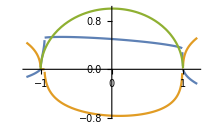

```mathematica
Plot[{Re[a],Im[a],c},{u2,-1.2,1.2}]
```

```mathematica
Solve[μ(1-μ) + d==0,μ]
```

{{μ→1/2 (1-√(1+4 d))},{μ→1/2 (1+√(1+4 d))}}

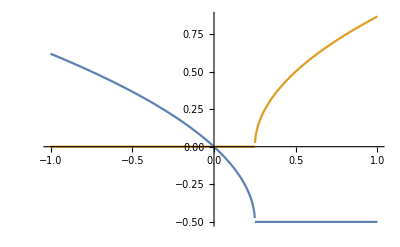

```mathematica
Plot[{Re[1/2 (-1+(1-4 d)^(1/2))],Im[1/2 (-1+(1-4 d)^(1/2))]},{d,-1,1}]
```

```mathematica
Eigenvalues[{{0,u/a},{b/a,-1}}]//FullSimplify
```

{-(a+√(a^2+4 b u))/(2 a),1/2 (-1+(√(a^2+4 b u))/a)}

```mathematica
1/2 (-1+(a √(1+4 b u/a^2))/a)
```

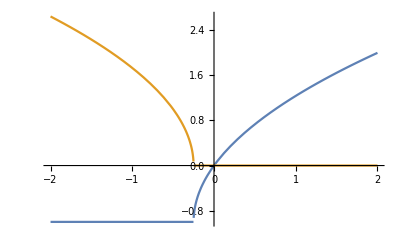

```mathematica
Plot[{Re[ (-1+√(1+4 d))],Im[ (-1+√(1+4 d))]},{d,-2,2}]
```

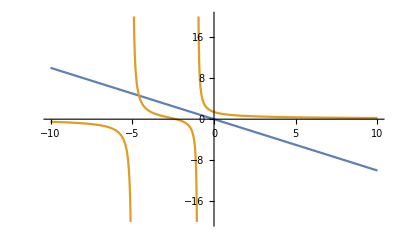

```mathematica
Plot[{-μ, 1/(μ+1)+2/(μ+5)},{μ,-10,10},PlotRange-> {-20,20}]
```